# FIST 2,2:

```mathematica
(*Latex dict*)Format[ga1]:=Subscript[γ,1];
Format[ga2]:=Subscript[γ,2];Format[be11]:=Subscript[β,11];
Format[mu]:=μ;Format[La1]:=Subscript[Λ,1];Format[La2]:=Subscript[Λ,2];
Format[de1]:=Subscript[δ,1];Format[de2]:=Subscript[δ,2];
Format[be12]:=Subscript[β,12];Format[be21]:=Subscript[β,21];Format[be22]:=Subscript[β,22];
Format[S1]:=Subscript[S,1];Format[S2]:=Subscript[S,2];
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];
AppendTo[$Path, FileNameJoin[{$HomeDirectory, "Dropbox", "EpidCRNmodels"}]];<<EpidCRN`;
```

```mathematica
?EpidCRN`*
```

```mathematica
RN = {
  0 -> "S1",0 -> "S2",
  "S1" + "I1" -> 2*"I1",
  "S1" + "I2" -> "I1" +"I2",
  "S2" + "I1" -> 2*"I1",
  "S2" + "I2" -> "I1" +"I2",
  "I1" -> "I2",
  "S1" -> 0,
  "S2" -> 0,
  "I1" -> 0,
  "I2" -> 0
};
rts={La1, La2,be11 I1 S1,be12 I2 S1, be21 I1 S2,be22 I2 S2,ga1 I1,mu S1,mu S2,(mu+de1)I1,
(mu+ga2+ de2)I2};
Print["reactions and transition rates: ",Transpose[{RN,rts}]//MatrixForm]
(*{RH,spe}=Take[reaToRHS[RN],2];*)
{spe, alp, bet, gam, Rv, RHS, def} = extMat[RN];var=ToExpression[spe];
Print["ga, be are: ",gam//MatrixForm," ",bet//MatrixForm];
```

reactions and transition rates: (0→S1 | Λ_1
0→S2 | Λ_2
I1+S1→2 I1 | β_11 I1 S_1
I2+S1→I1+I2 | β_12 I2 S_1
I1+S2→2 I1 | β_21 I1 S_2
I2+S2→I1+I2 | β_22 I2 S_2
I1→I2 | γ_1 I1
S1→0 | μ S_1
S2→0 | μ S_2
I1→0 | I1 (δ_1+μ)
I2→0 | I2 (δ_2+γ_2+μ))

Set::shape: Lists {spe,alp,bet,gam,Rv,RHS,def} and extMat[{0→S1,0→S2,I1+S1→2 I1,I2+S1→I1+I2,I1+S2→2 I1,I2+S2→I1+I2,I1→I2,S1→0,S2→0,I1→0,«1»}] are not the same shape.

ga, be are: gam bet

```mathematica
(*Verify the ODE system*)
{RHS, var, par, cp, mSi, Jx, Jy, E0, ngm,  R0A, EA,E1(* 
, E1t, E2t*)} = EpidCRN`bd1[RN, rts];
```

Set::shape: Lists {spe,alp,bet,gam,Rv,RHS,def} and extMat[{0→S1,0→S2,I1+S1→2 I1,I2+S1→I1+I2,I1+S2→2 I1,I2+S2→I1+I2,I1→I2,S1→0,S2→0,I1→0,«1»}] are not the same shape.

ga, be are: gam bet

reactions and transition rates: (0→S1 | Λ_1
0→S2 | Λ_2
I1+S1→2 I1 | β_11 I1 S_1
I2+S1→I1+I2 | β_12 I2 S_1
I1+S2→2 I1 | β_21 I1 S_2
I2+S2→I1+I2 | β_22 I2 S_2
I1→I2 | γ_1 I1
S1→0 | μ S_1
S2→0 | μ S_2
I1→0 | I1 (δ_1+μ)
I2→0 | I2 (δ_2+γ_2+μ))

Set::shape: Lists {RHS,var,par,cp,mSi,Jx,Jy,E0,ngm,R0A,«2»} and bd1[{0→S1,0→S2,I1+S1→2 I1,I2+S1→I1+I2,I1+S2→2 I1,I2+S2→I1+I2,I1→I2,S1→0,S2→0,I1→0,«1»},{Λ_1,Λ_2,β_11 I1 S_1,β_12 I2 S_1,β_21 I1 S_2,β_22 I2 S_2,γ_1 I1,μ S_1,μ S_2,I1 (δ_1+μ),«1»}] are not the same shape.

```mathematica
R0=R0A/.E0;coP=FindInstance[Append[cp,R0>1],par];v1=mu+ga1+de1;v2=mu+ga2+de2;Am={{-v1,0},{ga1,-v2}};
Bm={{be11,be12},{be21,be22}};
alp={1,0};muS=mu;BA=Bm.Inverse[-Am];
mR=Factor@BA.alp;Print["A inv=",Inverse[-Am]//MatrixForm," eigs= ",Am//Eigenvalues," dwell times= ",Dw=Inverse[-Am].alp//Factor," mR is ",mR];
ie=k*Dw;
R0=mR.{La1/mu,La2/mu};
SEE=Inverse[k DiagonalMatrix[ mR]+mu IdentityMatrix[2]].{La1,La2};
Lc=SEE. BA//Factor;
kpol=Collect[Numerator[Together[SEE.mR-1]],k];
(*Print["Lyapunov function coefs are",Lc];*)
LV=(#1 -#2 Log[#1])&;
xv={I1,I2};yv={S1,S2};
LVs=Total[yv-SEE*Log[yv]];
LVi=Lc.(yv-SEE*Log[yv]);
Lf=LVs+LVi;
LfD=Grad[Lf,var].RHS;
Print["Lie derivative is"];
LfDk=LfD/.coP//Simplify

(*cof=FullSimplify[#]&/@CoefficientList[-kpo,k]*)
```

A inv=(1/(δ_1+γ_1+μ) | 0
γ_1/((δ_1+γ_1+μ) (δ_2+γ_2+μ)) | 1/(δ_2+γ_2+μ)) eigs= {-δ_1-γ_1-μ,-δ_2-γ_2-μ} dwell times= {1/(δ_1+γ_1+μ),γ_1/((δ_1+γ_1+μ) (δ_2+γ_2+μ))} mR is {(β_11 δ_2+β_12 γ_1+β_11 γ_2+β_11 μ)/((δ_1+γ_1+μ) (δ_2+γ_2+μ)),(β_21 δ_2+β_22 γ_1+β_21 γ_2+β_21 μ)/((δ_1+γ_1+μ) (δ_2+γ_2+μ))}

Lie derivative is

{-(((9+8 k) (369+319 k+56 k^2) (-2+(2+2 I1+I2) S_1) (-18+(18+7 k) S_1))/S_1+(2 (18+7 k) (459+336 k+56 k^2) (-1+(1+I1+5 I2) S_2) (-9+(9+8 k) S_2))/S_2)/(2 (18+7 k)^2 (9+8 k)^2)}

```mathematica
so=Solve[kpo==0,k];so/.coE//N
kf=k/.so[[1]];ie=kf  Dw;
```

{{{k→0.3859},{k→-2.08233}}}

```mathematica
(*Lyapunov Verification with Numerical Endemic Finding*)verLyN[RHS_,var_,par_,cp_,E0_,R0A_,Lf_,kpol_,opts___]:=Module[{(*Plot control parameters*)contourRange=0.5,numContours=15,plotPoints=30,streamDensity=Fine,arrowSize=0.015,pointSize=0.02,testPoints=10,samplePoints=50,trajTime=10,initPerturb=0.2,(*Working variables*)R0,paramInstance,paramValues,R0val,RHSNum,DFEvals,initialGuess,endemicEq,endemicVals,zeroIndices,residual,LfNum,LfDNum,gradLf,gradAtEndemic,hessLf,hessAtEndemic,eigenHess,endemicPoint,LfAtEndemic,testPointsList,LfAtTestPoints,testPoints2,LfDAtTestPoints,negCount,LfPlot,grad1,grad2,val1,val2,contourP,streamP,plot2D,fixedVars,gradLfPlot,dynamicVars,odeSystem,initVals,init,sol,trajPlotNorm,finalState,userOpts,kpolN,kSol,kRule},(*Process optional arguments*)userOpts={opts};
If[Length[userOpts]>=1,contourRange=userOpts[[1]]];
If[Length[userOpts]>=2,numContours=userOpts[[2]]];
(*Compute R0*)R0=R0A/. E0;
Print["R0 expression: ",R0//Short];
(*Find parameter values using cp constraints and R0>1*)paramInstance=FindInstance[R0>1.5&&And@@cp,par,Reals];
If[Length[paramInstance]==0,Print["FindInstance failed with R0 > 1.5, trying R0 > 1.1"];
paramInstance=FindInstance[R0>1.1&&And@@cp,par,Reals];
If[Length[paramInstance]==0,Print["Could not find valid parameters"];
Return[$Failed]]];
paramValues=paramInstance[[1]];
Print["Parameters: ",paramValues];
R0val=R0/. paramValues//N;
Print["R0: ",R0val];
(*Find k using NSolve-the working version*)kpolN=kpol/. paramValues//N;
Print["kpol with parameters: ",kpolN];
kSol=NSolve[kpolN==0&&k>0,k];
Print["kSol: ",kSol];
If[Length[kSol]==0,Print["NSolve failed, trying Solve"];
kSol=Solve[kpolN==0,k]//N;
Print["Solve result: ",kSol];
(*Just take the last one for now*)kRule=Last[kSol],kRule=kSol[[1]]];
Print["k: ",k/. kRule];
(*Numerical RHS*)RHSNum=RHS/. paramValues;
(*DFE values*)DFEvals=var/. E0/. paramValues;
Print["DFE: ",DFEvals//N];
(*Find endemic equilibrium numerically*)initialGuess=MapThread[{#1,If[#2==0,0.1,#2*0.8]}&,{var,DFEvals}];
endemicEq=FindRoot[Thread[RHSNum==0],initialGuess,Method->"Newton",AccuracyGoal->10,PrecisionGoal->10];
endemicVals=var/. endemicEq;
(*Check if we found endemic (not DFE)*)zeroIndices=Position[DFEvals,0]//Flatten;
If[Length[zeroIndices]>0&&Max[Abs[endemicVals[[zeroIndices]]]]<10^-6,Print["First attempt converged to DFE, trying alternative"];
endemicEq=FindRoot[Thread[RHSNum==0],Thread[{var,ConstantArray[1.0,Length[var]]}],Method->"Newton"];
endemicVals=var/. endemicEq];
(*Verify endemic*)If[Length[zeroIndices]>0&&Max[Abs[endemicVals[[zeroIndices]]]]<10^-6,Print["Warning: Could not find endemic equilibrium"];
Return[$Failed]];
Print["Endemic found: ",Thread[var->endemicVals]//N];
residual=RHSNum/. Thread[var->endemicVals];
Print["Equilibrium residual norm: ",Norm[residual]//N];
(*Lyapunov function analysis*)LfNum=Lf/. kRule/. paramValues;
(*Compute LfD as Lie derivative:Grad[Lf,var].RHS*)LfDNum=Grad[LfNum,var].RHSNum;
(*Check critical point*)gradLf=Grad[LfNum,var];
gradAtEndemic=gradLf/. Thread[var->endemicVals]//N//Chop;
Print["||grad||: ",Norm[gradAtEndemic]//N];
(*Hessian analysis*)hessLf=D[LfNum,{var,2}];
hessAtEndemic=hessLf/. Thread[var->endemicVals];
eigenHess=Eigenvalues[hessAtEndemic//N];
Print["Hess eigs: ",eigenHess];
Print["min eig: ",Min[eigenHess]," (positive = local minimum)"];
(*Lyapunov values*)endemicPoint=Thread[var->endemicVals];
LfAtEndemic=LfNum/. endemicPoint;
Print["Lf(endemic): ",LfAtEndemic//N];
(*Test around endemic*)testPointsList=Table[Thread[var->endemicVals*(1+0.3*RandomReal[{-1,1},Length[var]])],{testPoints}];
LfAtTestPoints=Table[LfNum/. pt,{pt,testPointsList}];
Print["Lf test range: [",Min[LfAtTestPoints]//N,", ",Max[LfAtTestPoints]//N,"]"];
(*Lie derivative test*)Print["LfD(endemic): ",(LfDNum/. endemicPoint)//N//Chop];
testPoints2=Table[Thread[var->RandomReal[{0.1,2}]*endemicVals],{samplePoints}];
LfDAtTestPoints=Table[LfDNum/. pt,{pt,testPoints2}];
negCount=Count[LfDAtTestPoints,x_/;x<=0];
Print["LfD: max=",Max[LfDAtTestPoints]//N," neg=",negCount,"/",samplePoints];
(*2D Plot with gradient flow*)If[Length[var]>=2,fixedVars=Thread[Drop[var,2]->Drop[endemicVals,2]];
LfPlot[x_,y_]:=Evaluate[LfNum/. fixedVars/. {var[[1]]->x,var[[2]]->y}];
gradLfPlot=Grad[LfNum/. fixedVars,{var[[1]],var[[2]]}];
grad1[x_,y_]:=Evaluate[gradLfPlot[[1]]/. {var[[1]]->x,var[[2]]->y}];
grad2[x_,y_]:=Evaluate[gradLfPlot[[2]]/. {var[[1]]->x,var[[2]]->y}];
val1=endemicVals[[1]];
val2=endemicVals[[2]];
contourP=ContourPlot[LfPlot[x,y],{x,(1-contourRange)*val1,(1+contourRange)*val1},{y,(1-contourRange)*val2,(1+contourRange)*val2},Contours->numContours,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotPoints->plotPoints];
streamP=StreamPlot[{-grad1[x,y],-grad2[x,y]},{x,(1-contourRange)*val1,(1+contourRange)*val1},{y,(1-contourRange)*val2,(1+contourRange)*val2},StreamStyle->{Black,Arrowheads[arrowSize]},StreamPoints->streamDensity];
plot2D=Show[contourP,streamP,Epilog->{Red,PointSize[pointSize],Point[{val1,val2}]},PlotLabel->"Lyapunov function with gradient flow",FrameLabel->{ToString[var[[1]]],ToString[var[[2]]]}];
Print[plot2D]];
(*Trajectory simulation*)dynamicVars=Table[Unique["v"][t],{Length[var]}];
odeSystem=MapThread[#1'[t]==(#2/. Thread[var->#3]/. paramValues)&,{Head/@dynamicVars,RHS,dynamicVars}];
initVals=endemicVals*(1+initPerturb*RandomReal[{-0.5,0.5},Length[var]]);
init=MapThread[#1[0]==#2&,{Head/@dynamicVars,initVals}];
sol=NDSolve[Join[odeSystem,init],Head/@dynamicVars,{t,0,trajTime}];
trajPlotNorm=Plot[Evaluate[(dynamicVars/. sol[[1]])/initVals],{t,0,trajTime},PlotLabel->"Normalized Trajectories (X(t)/X(0))",AxesLabel->{"Time","X(t)/X(0)"},PlotLegends->(ToString[#,TraditionalForm]&)/@var,PlotStyle->ColorData[97,"ColorList"][[1;;Length[var]]],PlotRange->All];
Print[trajPlotNorm];
finalState=(dynamicVars/. t->trajTime)/. sol[[1]];
Print["Final state: ",finalState//N];
Print["Distance to endemic: ",Norm[finalState-endemicVals]//N]]
(*verLyN[RHS,var,par,cp,E0,R0A,Lf,kpol]*)
```

R0 expression: {(β_11 Λ_1+β_21 Λ_2+(«1»)/μ+«1»«1»«1»+(«1»)/μ+(«1»)/μ+(β_21 γ_2 Λ_2)/μ)/((δ_1+γ_1+μ) (δ_2+γ_2+μ))}

Parameters: {β_11→1.125,β_12→1.6875,β_21→1.125,β_22→6.75,δ_1→1.,δ_2→1.,γ_1→1.,γ_2→1.,Λ_1→1.,Λ_2→1.,μ→1.}

R0: {1.6875}

kpol with parameters: 55.6875-34.1719 k-51.2578 k^2

kSol: {{k→0.760984}}

k: 0.760984

DFE: {1.,1.,0.,0.}

Endemic found: {S_1→0.700254,S_2→0.538762,I1→0.253661,I2→0.0845538}

Equilibrium residual norm: 1.24127×10^-16

||grad||: 0.

Hess eigs: {4.83721,2.85611,0.,0.}

min eig: 0. (positive = local minimum)

Lf(endemic): 4.17199

Lf test range: [4.18024, 4.28997]

LfD(endemic): 0

LfD: max=-0.000438569 neg=50/50

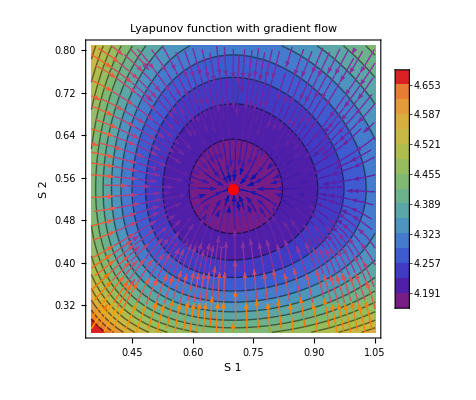

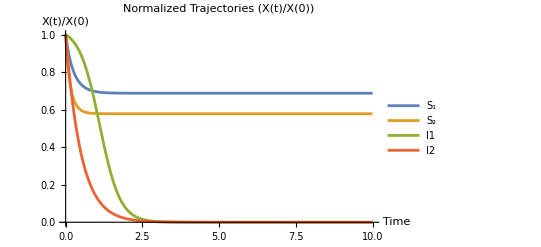

Final state: {0.444444,0.298468,7.16221×10^-13,1.25567×10^-10}

Distance to endemic: 0.441218

```mathematica
verLyN[RHS,var,par,cp,E0,R0A,Lf,kpol]
```

#### Check of the injectivity of SI2:

```mathematica
jac=Grad[RHS,var];
det=Det[jac]//FullSimplify;
Print["det=", det]
Reduce[Join[cp,Thread[var>0],{det<0}]]//FullSimplify
```

det=(-k6+k3 x1) (k4 (k5-k2 x1)+k2 k5 x2)+k3 k6 (-k5+k2 x1) x3

k1>0&&x1>0&&k6>0&&x2>0&&x3>0&&((k2>0&&k4>0&&((k5>0&&k2<(k5 (k4 (k6-k3 x1)+k3 k6 x3))/((k6-k3 x1) (k4 x1-k5 x2)+k3 k6 x1 x3)&&(k3==k6/x1||(k3>0&&k3<k6/x1)||(k3>k6/x1&&k4<(k3 k6 x3)/(-k6+k3 x1))))||(k3>0&&k5≥(x1 (k4+(k3 k6 x3)/(k6-k3 x1)))/x2&&k3<k6/x1)))||(k5<(x1 (k4+(k3 k6 x3)/(k6-k3 x1)))/x2&&k2>(k5 (k4 (k6-k3 x1)+k3 k6 x3))/((k6-k3 x1) (k4 x1-k5 x2)+k3 k6 x1 x3)&&k3>k6/x1&&k4>(k3 k6 x3)/(-k6+k3 x1)&&k5>0))